```mathematica
Clear["Global`*"]
```

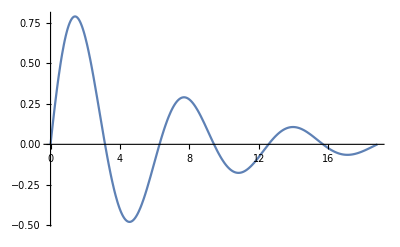

(4 (-1+ⅇ^3) π^2)/(ⅇ^3 (1+4 π^2))

```mathematica
f[x_]:=Exp[(-Abs[x])/(2π)]Sin[x]
Plot[f[x],{x,0,6π}]
exactValue=Integrate[f[x],{x,0,6π}]
```

```mathematica
simpsonCoefficients={1/3,4/3,2/3}
trapezCoefficients={1/2,1}
Simpson[f_,a_,b_,n_]:=(b-a)/n(f[a]simpsonCoefficients[[1]]+
Sum[N[f[a+i(b-a)/n]]simpsonCoefficients[[ 2+Mod[i+1,2] ]],{i,1,n-1}]
+f[b] simpsonCoefficients[[1]])/.n->n+Mod[n,2]
Trapez[f_,a_,b_,n_]:=(b-a)/n(f[a]trapezCoefficients[[1]]+
Sum[N[f[a+i(b-a)/n]]trapezCoefficients[[ 2+Mod[i+1,1] ]],{i,1,n-1}]
+f[b] trapezCoefficients[[1]])/.n->n+Mod[n,2]
```

{1/3,4/3,2/3}

{1/2,1}

```mathematica
trapezDeviations={#,Abs[Trapez[f,0,6π,#]-exactValue]}&/@Range[100,1000,100];
simpsonDeviations={#,Abs[Simpson[f,0,6π,#]-exactValue]}&/@Range[100,1000,100];
```

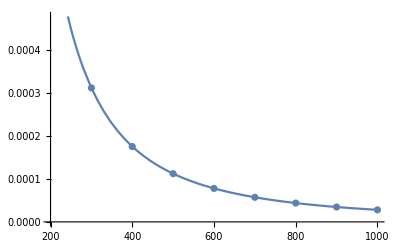

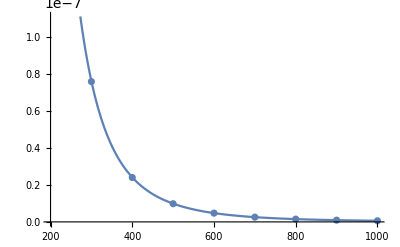

```mathematica
fitAndPlot[data_,exponent_]:=
Show[Plot[NonlinearModelFit[data,b(x)^-exponent,{b},x][y],{y,200,1000}],ListPlot[data]]
fitAndPlot[trapezDeviations,2]
fitAndPlot[simpsonDeviations/.{n_,d_}:>{n,d},4]
```

```mathematica
potentials={Abs[#]&,4#^2&,#^4&,1-2#^2+#^4&};
```

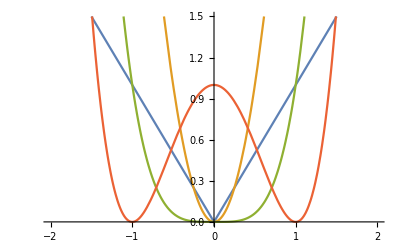

```mathematica
Plot[Evaluate[#1[x]&/@potentials],{x,-2,2},PlotRange->{0,1.5}]
```

```mathematica
T[v_,e_]:=Module[{reversal=NSolve[v[x0]==e,x0,Reals]},Sqrt[2] NIntegrate[1/Sqrt[e-v[x]],{x,x0/.reversal[[1]],x0/.reversal[[2]]}]]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

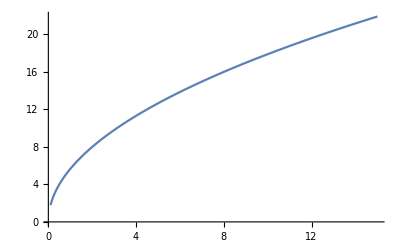
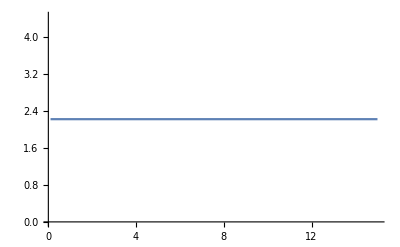

```mathematica
Texact[v_,e_]:=Module[{reversal=Solve[v[x0]==e,x0]},Sqrt[2] Integrate[1/Sqrt[e-v[x]],{x,x0/.reversal[[1]],x0/.reversal[[2]]},Assumptions->e>0]]

Plot[#,{e,0.1,15}]&/@Evaluate[Texact[#,e]&/@potentials[[1;;2]]]
```

```mathematica
vals=Table[{e,T[potentials[[v]],e]},{v,1,4},{e,0.1,15,.1}];//Quiet
```

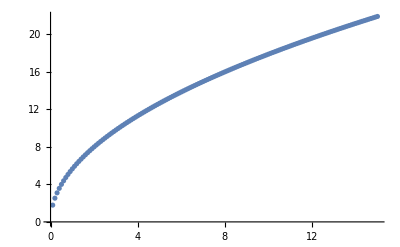
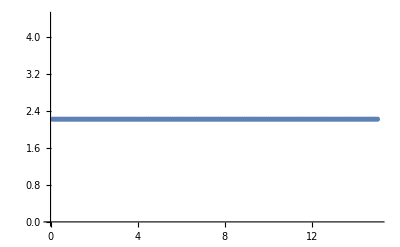
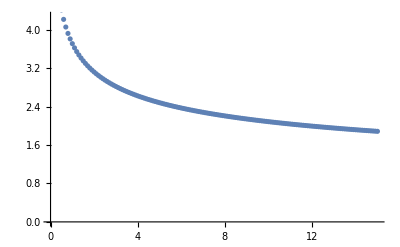
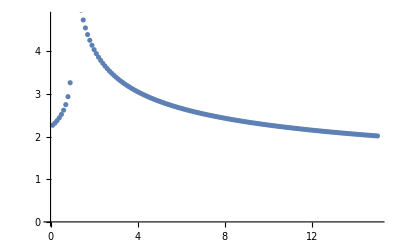

```mathematica
ListPlot[#]&/@vals
```

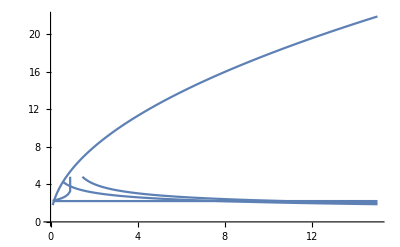

```mathematica
Show[ListLinePlot[#]&/@vals]
```

```mathematica
√8//N
```

2.82843